# S2S Data Cutting

## Slide Show Subtitle

BX Pan
2017.9.27

Environment Setting

```mathematica
controlDirectory="/Volumes/lambda/Data/S2S/Control/";
pertubationDirectory="/Volumes/lambda/Data/S2S/Pertubation/";
```

```mathematica
polygon=Block[{westconus},
	westconus=Block[{ow,ca},
	ow=Import["/Users/lambda/Documents/Data/GeoDivision/CONUS/oregonwashington.mx"];
	ca=Import["/Users/lambda/Documents/Data/GeoDivision/CONUS/california.mx"];
	Polygon[Flatten[{ow[[1]],ca[[1]]},1]]];
	westconus[[1]]];
(*polygon in the form of {subpoly1,subpoly2,...},subpoly in th form of {{long1,lat1},{long2,lat2}...}*)
```

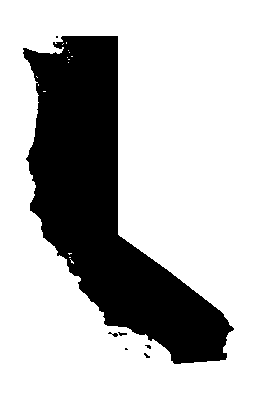

```mathematica
Graphics[Polygon[polygon]]
```

```mathematica
dataset="ECCC";
SetDirectory["/Volumes/lambda/Data/S2S/Control/"<>dataset];
 sample=FileNames["*.nc"][[1]];
 points=Block[{s2sprecip,s2slat,s2slon,s2stime,p,indexes},
	{s2sprecip,s2slat,s2slon,s2stime}=Map[Import[sample,{"Datasets",#}]&,{"tp","latitude","longitude","time"}];
    p=Block[{InOrOut,grids},
        InOrOut[point_]:=Block[{singletest},
			singletest[poly_] := Round[(Total@ Mod[(# - RotateRight[#]) &@(ArcTan @@ (point - #) & /@ poly), 2 Pi, -Pi]/2/Pi)] != 0;
			(Map[singletest,polygon])/.List->Or];
        grids=Block[{scope=Map[MinMax,Transpose[Flatten[polygon,1]]],lat,lon},
            lat=Select[s2slat,And[#<=scope[[2,2]], #>=scope[[2,1]]]&];
            lon=Select[s2slon,And[#<=scope[[1,2]], #>=scope[[1,1]]]&];
        Table[Table[{lat[[i]],lon[[j]]},{j,Length[lon]}],{i,Length[lat]}]];
        Select[Flatten[grids,1],InOrOut[Reverse[#]]&]];
    indexes=Block[{grids=Table[Table[{s2slat[[i]],s2slon[[j]]},{j,Length[s2slon]}],{i,Length[s2slat]}]},
        Map[Position[grids,#][[1]]&,p]];
    indexes];
 files=FileNames["*.nc"];
result=Map[Block[{d=Import[#,{"Datasets","tp"}]},
          Table[d[[;;,points[[jj,1]],points[[jj,2]]]],{jj,Length[points]}]]&,files];
Export[dataset<>".mx",result]
```

S2SCut

```mathematica
S2Scut[polygon_,dataset_,class_]:=Block[{points,sample,result,files},
 SetDirectory["/Volumes/lambda/Data/S2S/Control/"<>dataset];
 sample=FileNames["*.nc"][[1]];
 points=Block[{s2sprecip,s2slat,s2slon,s2stime,p,indexes},
	{s2sprecip,s2slat,s2slon,s2stime}=Map[Import[sample,{"Datasets",#}]&,{"tp","latitude","longitude","time"}];
    p=Block[{InOrOut,grids},
        InOrOut[point_]:=Block[{singletest},
			singletest[poly_] := Round[(Total@ Mod[(# - RotateRight[#]) &@(ArcTan @@ (point - #) & /@ poly), 2 Pi, -Pi]/2/Pi)] != 0;
			(Map[singletest,polygon])/.List->Or];
        grids=Block[{scope=Map[MinMax,Transpose[Flatten[polygon,1]]],lat,lon},
            lat=Select[s2slat,And[#<=scope[[2,2]], #>=scope[[2,1]]]&];
            lon=Select[s2slon,And[#<=scope[[1,2]], #>=scope[[1,1]]]&];
        Table[Table[{lat[[i]],lon[[j]]},{j,Length[lon]}],{i,Length[lat]}]];
        Select[Flatten[grids,1],InOrOut[Reverse[#]]&]];
    indexes=Block[{grids=Table[Table[{s2slat[[i]],s2slon[[j]]},{j,Length[s2slon]}],{i,Length[s2slat]}]},
        Map[Position[grids,#][[1]]&,p]];
    indexes];
 files=FileNames["*.nc"];
 result=Map[Block[{d=Import[#,{"Datasets","tp"}]},
          Table[d[[;;,points[[jj,1]],points[[jj,2]]]],{jj,Length[points]}]]&,files];
 Export[dataset<>".mx",result];
 dataset];
```

```mathematica
SetDirectory["/Volumes/lambda/Data/S2S/Control/"];
names=FileNames[][[{4,5,6,7,8,9,10,11}]]
```

{BoM,ECCC,ECMWF,HCMR,ISACCNR,JMA,KMA,MeteoFrance,NCEP,UKMO}

```mathematica
Map[S2Scut[polygon,#,"Control"]&,names];
```